```mathematica
(Table[Mod[n^k,#],{n,1,#},{k,1,#}]//MatrixForm)&/@Range[10]
```

{(0),(1 | 1
0 | 0),(1 | 1 | 1
2 | 1 | 2
0 | 0 | 0),(1 | 1 | 1 | 1
2 | 0 | 0 | 0
3 | 1 | 3 | 1
0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1
2 | 4 | 3 | 1 | 2
3 | 4 | 2 | 1 | 3
4 | 1 | 4 | 1 | 4
0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 2 | 4 | 2 | 4
3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 4
5 | 1 | 5 | 1 | 5 | 1
0 | 0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 1 | 2 | 4 | 1 | 2
3 | 2 | 6 | 4 | 5 | 1 | 3
4 | 2 | 1 | 4 | 2 | 1 | 4
5 | 4 | 6 | 2 | 3 | 1 | 5
6 | 1 | 6 | 1 | 6 | 1 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 0 | 0 | 0 | 0 | 0 | 0
3 | 1 | 3 | 1 | 3 | 1 | 3 | 1
4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 5 | 1 | 5 | 1 | 5 | 1
6 | 4 | 0 | 0 | 0 | 0 | 0 | 0
7 | 1 | 7 | 1 | 7 | 1 | 7 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 7 | 5 | 1 | 2 | 4 | 8
3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 7 | 1 | 4 | 7 | 1 | 4 | 7 | 1
5 | 7 | 8 | 4 | 2 | 1 | 5 | 7 | 8
6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 4 | 1 | 7 | 4 | 1 | 7 | 4 | 1
8 | 1 | 8 | 1 | 8 | 1 | 8 | 1 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 6 | 2 | 4 | 8 | 6 | 2 | 4
3 | 9 | 7 | 1 | 3 | 9 | 7 | 1 | 3 | 9
4 | 6 | 4 | 6 | 4 | 6 | 4 | 6 | 4 | 6
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6
7 | 9 | 3 | 1 | 7 | 9 | 3 | 1 | 7 | 9
8 | 4 | 2 | 6 | 8 | 4 | 2 | 6 | 8 | 4
9 | 1 | 9 | 1 | 9 | 1 | 9 | 1 | 9 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
(Table[Mod[n^k,#],{n,1,#},{k,1,#}]//MatrixForm)&/@Prime[Range[9]]
```

{(1 | 1
0 | 0),(1 | 1 | 1
2 | 1 | 2
0 | 0 | 0),(1 | 1 | 1 | 1 | 1
2 | 4 | 3 | 1 | 2
3 | 4 | 2 | 1 | 3
4 | 1 | 4 | 1 | 4
0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 1 | 2 | 4 | 1 | 2
3 | 2 | 6 | 4 | 5 | 1 | 3
4 | 2 | 1 | 4 | 2 | 1 | 4
5 | 4 | 6 | 2 | 3 | 1 | 5
6 | 1 | 6 | 1 | 6 | 1 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 5 | 10 | 9 | 7 | 3 | 6 | 1 | 2
3 | 9 | 5 | 4 | 1 | 3 | 9 | 5 | 4 | 1 | 3
4 | 5 | 9 | 3 | 1 | 4 | 5 | 9 | 3 | 1 | 4
5 | 3 | 4 | 9 | 1 | 5 | 3 | 4 | 9 | 1 | 5
6 | 3 | 7 | 9 | 10 | 5 | 8 | 4 | 2 | 1 | 6
7 | 5 | 2 | 3 | 10 | 4 | 6 | 9 | 8 | 1 | 7
8 | 9 | 6 | 4 | 10 | 3 | 2 | 5 | 7 | 1 | 8
9 | 4 | 3 | 5 | 1 | 9 | 4 | 3 | 5 | 1 | 9
10 | 1 | 10 | 1 | 10 | 1 | 10 | 1 | 10 | 1 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 3 | 6 | 12 | 11 | 9 | 5 | 10 | 7 | 1 | 2
3 | 9 | 1 | 3 | 9 | 1 | 3 | 9 | 1 | 3 | 9 | 1 | 3
4 | 3 | 12 | 9 | 10 | 1 | 4 | 3 | 12 | 9 | 10 | 1 | 4
5 | 12 | 8 | 1 | 5 | 12 | 8 | 1 | 5 | 12 | 8 | 1 | 5
6 | 10 | 8 | 9 | 2 | 12 | 7 | 3 | 5 | 4 | 11 | 1 | 6
7 | 10 | 5 | 9 | 11 | 12 | 6 | 3 | 8 | 4 | 2 | 1 | 7
8 | 12 | 5 | 1 | 8 | 12 | 5 | 1 | 8 | 12 | 5 | 1 | 8
9 | 3 | 1 | 9 | 3 | 1 | 9 | 3 | 1 | 9 | 3 | 1 | 9
10 | 9 | 12 | 3 | 4 | 1 | 10 | 9 | 12 | 3 | 4 | 1 | 10
11 | 4 | 5 | 3 | 7 | 12 | 2 | 9 | 8 | 10 | 6 | 1 | 11
12 | 1 | 12 | 1 | 12 | 1 | 12 | 1 | 12 | 1 | 12 | 1 | 12
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 15 | 13 | 9 | 1 | 2 | 4 | 8 | 16 | 15 | 13 | 9 | 1 | 2
3 | 9 | 10 | 13 | 5 | 15 | 11 | 16 | 14 | 8 | 7 | 4 | 12 | 2 | 6 | 1 | 3
4 | 16 | 13 | 1 | 4 | 16 | 13 | 1 | 4 | 16 | 13 | 1 | 4 | 16 | 13 | 1 | 4
5 | 8 | 6 | 13 | 14 | 2 | 10 | 16 | 12 | 9 | 11 | 4 | 3 | 15 | 7 | 1 | 5
6 | 2 | 12 | 4 | 7 | 8 | 14 | 16 | 11 | 15 | 5 | 13 | 10 | 9 | 3 | 1 | 6
7 | 15 | 3 | 4 | 11 | 9 | 12 | 16 | 10 | 2 | 14 | 13 | 6 | 8 | 5 | 1 | 7
8 | 13 | 2 | 16 | 9 | 4 | 15 | 1 | 8 | 13 | 2 | 16 | 9 | 4 | 15 | 1 | 8
9 | 13 | 15 | 16 | 8 | 4 | 2 | 1 | 9 | 13 | 15 | 16 | 8 | 4 | 2 | 1 | 9
10 | 15 | 14 | 4 | 6 | 9 | 5 | 16 | 7 | 2 | 3 | 13 | 11 | 8 | 12 | 1 | 10
11 | 2 | 5 | 4 | 10 | 8 | 3 | 16 | 6 | 15 | 12 | 13 | 7 | 9 | 14 | 1 | 11
12 | 8 | 11 | 13 | 3 | 2 | 7 | 16 | 5 | 9 | 6 | 4 | 14 | 15 | 10 | 1 | 12
13 | 16 | 4 | 1 | 13 | 16 | 4 | 1 | 13 | 16 | 4 | 1 | 13 | 16 | 4 | 1 | 13
14 | 9 | 7 | 13 | 12 | 15 | 6 | 16 | 3 | 8 | 10 | 4 | 5 | 2 | 11 | 1 | 14
15 | 4 | 9 | 16 | 2 | 13 | 8 | 1 | 15 | 4 | 9 | 16 | 2 | 13 | 8 | 1 | 15
16 | 1 | 16 | 1 | 16 | 1 | 16 | 1 | 16 | 1 | 16 | 1 | 16 | 1 | 16 | 1 | 16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 13 | 7 | 14 | 9 | 18 | 17 | 15 | 11 | 3 | 6 | 12 | 5 | 10 | 1 | 2
3 | 9 | 8 | 5 | 15 | 7 | 2 | 6 | 18 | 16 | 10 | 11 | 14 | 4 | 12 | 17 | 13 | 1 | 3
4 | 16 | 7 | 9 | 17 | 11 | 6 | 5 | 1 | 4 | 16 | 7 | 9 | 17 | 11 | 6 | 5 | 1 | 4
5 | 6 | 11 | 17 | 9 | 7 | 16 | 4 | 1 | 5 | 6 | 11 | 17 | 9 | 7 | 16 | 4 | 1 | 5
6 | 17 | 7 | 4 | 5 | 11 | 9 | 16 | 1 | 6 | 17 | 7 | 4 | 5 | 11 | 9 | 16 | 1 | 6
7 | 11 | 1 | 7 | 11 | 1 | 7 | 11 | 1 | 7 | 11 | 1 | 7 | 11 | 1 | 7 | 11 | 1 | 7
8 | 7 | 18 | 11 | 12 | 1 | 8 | 7 | 18 | 11 | 12 | 1 | 8 | 7 | 18 | 11 | 12 | 1 | 8
9 | 5 | 7 | 6 | 16 | 11 | 4 | 17 | 1 | 9 | 5 | 7 | 6 | 16 | 11 | 4 | 17 | 1 | 9
10 | 5 | 12 | 6 | 3 | 11 | 15 | 17 | 18 | 9 | 14 | 7 | 13 | 16 | 8 | 4 | 2 | 1 | 10
11 | 7 | 1 | 11 | 7 | 1 | 11 | 7 | 1 | 11 | 7 | 1 | 11 | 7 | 1 | 11 | 7 | 1 | 11
12 | 11 | 18 | 7 | 8 | 1 | 12 | 11 | 18 | 7 | 8 | 1 | 12 | 11 | 18 | 7 | 8 | 1 | 12
13 | 17 | 12 | 4 | 14 | 11 | 10 | 16 | 18 | 6 | 2 | 7 | 15 | 5 | 8 | 9 | 3 | 1 | 13
14 | 6 | 8 | 17 | 10 | 7 | 3 | 4 | 18 | 5 | 13 | 11 | 2 | 9 | 12 | 16 | 15 | 1 | 14
15 | 16 | 12 | 9 | 2 | 11 | 13 | 5 | 18 | 4 | 3 | 7 | 10 | 17 | 8 | 6 | 14 | 1 | 15
16 | 9 | 11 | 5 | 4 | 7 | 17 | 6 | 1 | 16 | 9 | 11 | 5 | 4 | 7 | 17 | 6 | 1 | 16
17 | 4 | 11 | 16 | 6 | 7 | 5 | 9 | 1 | 17 | 4 | 11 | 16 | 6 | 7 | 5 | 9 | 1 | 17
18 | 1 | 18 | 1 | 18 | 1 | 18 | 1 | 18 | 1 | 18 | 1 | 18 | 1 | 18 | 1 | 18 | 1 | 18
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 9 | 18 | 13 | 3 | 6 | 12 | 1 | 2 | 4 | 8 | 16 | 9 | 18 | 13 | 3 | 6 | 12 | 1 | 2
3 | 9 | 4 | 12 | 13 | 16 | 2 | 6 | 18 | 8 | 1 | 3 | 9 | 4 | 12 | 13 | 16 | 2 | 6 | 18 | 8 | 1 | 3
4 | 16 | 18 | 3 | 12 | 2 | 8 | 9 | 13 | 6 | 1 | 4 | 16 | 18 | 3 | 12 | 2 | 8 | 9 | 13 | 6 | 1 | 4
5 | 2 | 10 | 4 | 20 | 8 | 17 | 16 | 11 | 9 | 22 | 18 | 21 | 13 | 19 | 3 | 15 | 6 | 7 | 12 | 14 | 1 | 5
6 | 13 | 9 | 8 | 2 | 12 | 3 | 18 | 16 | 4 | 1 | 6 | 13 | 9 | 8 | 2 | 12 | 3 | 18 | 16 | 4 | 1 | 6
7 | 3 | 21 | 9 | 17 | 4 | 5 | 12 | 15 | 13 | 22 | 16 | 20 | 2 | 14 | 6 | 19 | 18 | 11 | 8 | 10 | 1 | 7
8 | 18 | 6 | 2 | 16 | 13 | 12 | 4 | 9 | 3 | 1 | 8 | 18 | 6 | 2 | 16 | 13 | 12 | 4 | 9 | 3 | 1 | 8
9 | 12 | 16 | 6 | 8 | 3 | 4 | 13 | 2 | 18 | 1 | 9 | 12 | 16 | 6 | 8 | 3 | 4 | 13 | 2 | 18 | 1 | 9
10 | 8 | 11 | 18 | 19 | 6 | 14 | 2 | 20 | 16 | 22 | 13 | 15 | 12 | 5 | 4 | 17 | 9 | 21 | 3 | 7 | 1 | 10
11 | 6 | 20 | 13 | 5 | 9 | 7 | 8 | 19 | 2 | 22 | 12 | 17 | 3 | 10 | 18 | 14 | 16 | 15 | 4 | 21 | 1 | 11
12 | 6 | 3 | 13 | 18 | 9 | 16 | 8 | 4 | 2 | 1 | 12 | 6 | 3 | 13 | 18 | 9 | 16 | 8 | 4 | 2 | 1 | 12
13 | 8 | 12 | 18 | 4 | 6 | 9 | 2 | 3 | 16 | 1 | 13 | 8 | 12 | 18 | 4 | 6 | 9 | 2 | 3 | 16 | 1 | 13
14 | 12 | 7 | 6 | 15 | 3 | 19 | 13 | 21 | 18 | 22 | 9 | 11 | 16 | 17 | 8 | 20 | 4 | 10 | 2 | 5 | 1 | 14
15 | 18 | 17 | 2 | 7 | 13 | 11 | 4 | 14 | 3 | 22 | 8 | 5 | 6 | 21 | 16 | 10 | 12 | 19 | 9 | 20 | 1 | 15
16 | 3 | 2 | 9 | 6 | 4 | 18 | 12 | 8 | 13 | 1 | 16 | 3 | 2 | 9 | 6 | 4 | 18 | 12 | 8 | 13 | 1 | 16
17 | 13 | 14 | 8 | 21 | 12 | 20 | 18 | 7 | 4 | 22 | 6 | 10 | 9 | 15 | 2 | 11 | 3 | 5 | 16 | 19 | 1 | 17
18 | 2 | 13 | 4 | 3 | 8 | 6 | 16 | 12 | 9 | 1 | 18 | 2 | 13 | 4 | 3 | 8 | 6 | 16 | 12 | 9 | 1 | 18
19 | 16 | 5 | 3 | 11 | 2 | 15 | 9 | 10 | 6 | 22 | 4 | 7 | 18 | 20 | 12 | 21 | 8 | 14 | 13 | 17 | 1 | 19
20 | 9 | 19 | 12 | 10 | 16 | 21 | 6 | 5 | 8 | 22 | 3 | 14 | 4 | 11 | 13 | 7 | 2 | 17 | 18 | 15 | 1 | 20
21 | 4 | 15 | 16 | 14 | 18 | 10 | 3 | 17 | 12 | 22 | 2 | 19 | 8 | 7 | 9 | 5 | 13 | 20 | 6 | 11 | 1 | 21
22 | 1 | 22 | 1 | 22 | 1 | 22 | 1 | 22 | 1 | 22 | 1 | 22 | 1 | 22 | 1 | 22 | 1 | 22 | 1 | 22 | 1 | 22
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

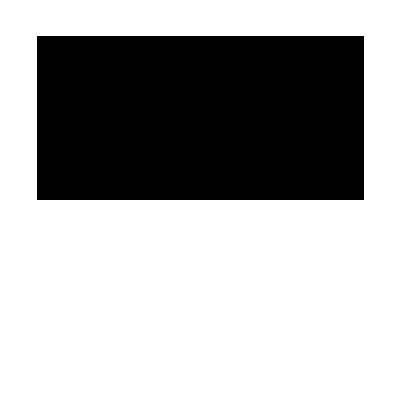
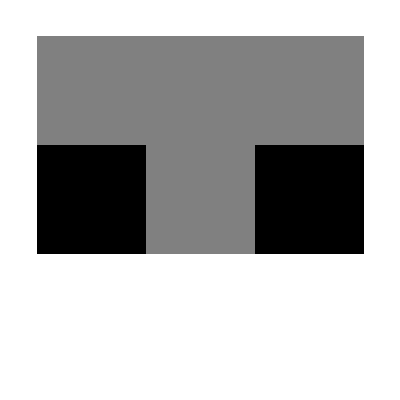
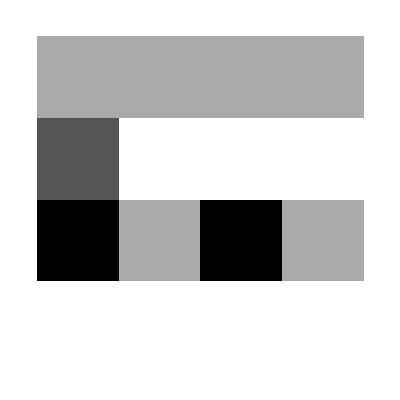
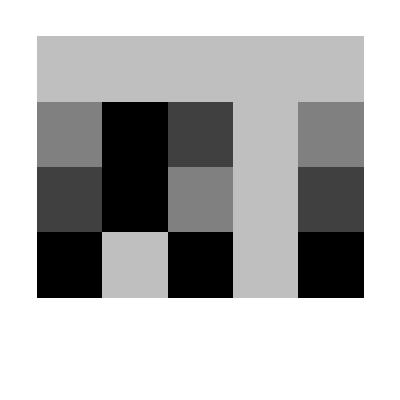
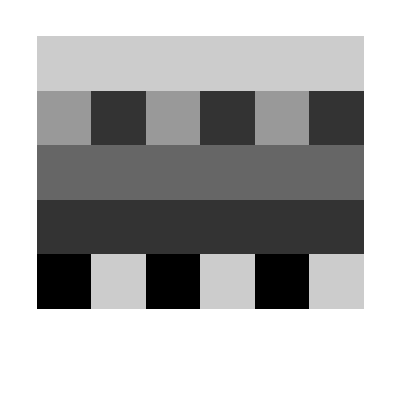
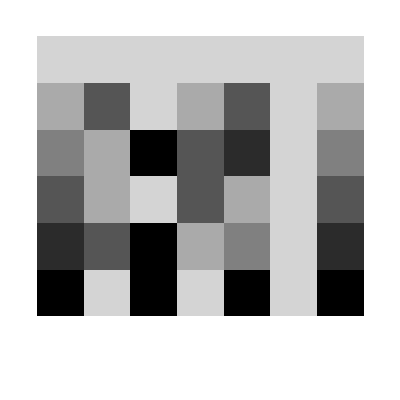
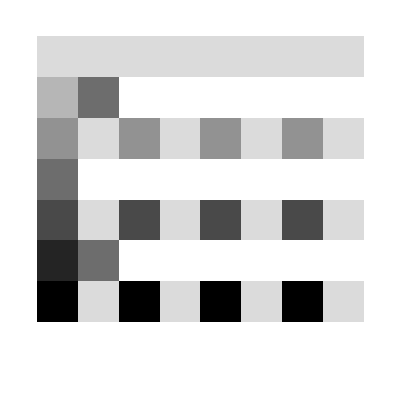
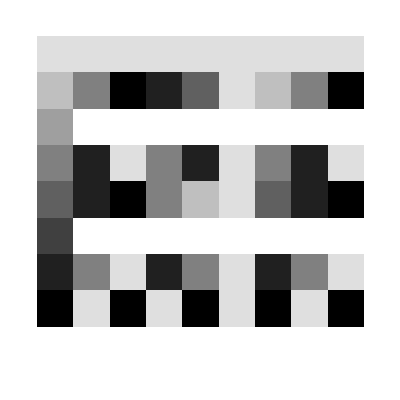
0 | 1 | -Graphics-
1 | 2 | -Graphics-
1 | 3 | -Graphics-
0 | 4 | -Graphics-
1 | 5 | -Graphics-
0 | 6 | -Graphics-
1 | 7 | -Graphics-
0 | 8 | -Graphics-
0 | 9 | -Graphics-
0 | 10 | -Graphics-
1 | 11 | -Graphics-
0 | 12 | -Graphics-
1 | 13 | -Graphics-
0 | 14 | -Graphics-
0 | 15 | -Graphics-
0 | 16 | -Graphics-
1 | 17 | -Graphics-
0 | 18 | -Graphics-
1 | 19 | -Graphics-
0 | 20 | -Graphics-
0 | 21 | -Graphics-
0 | 22 | -Graphics-
1 | 23 | -Graphics-
0 | 24 | -Graphics-
0 | 25 | -Graphics-
0 | 26 | -Graphics-
0 | 27 | -Graphics-
0 | 28 | -Graphics-
1 | 29 | -Graphics-
0 | 30 | -Graphics-
1 | 31 | -Graphics-
0 | 32 | -Graphics-
0 | 33 | -Graphics-
0 | 34 | -Graphics-
0 | 35 | -Graphics-
0 | 36 | -Graphics-
1 | 37 | -Graphics-
0 | 38 | -Graphics-
0 | 39 | -Graphics-
0 | 40 | -Graphics-
1 | 41 | -Graphics-
0 | 42 | -Graphics-
1 | 43 | -Graphics-
0 | 44 | -Graphics-
0 | 45 | -Graphics-
0 | 46 | -Graphics-
1 | 47 | -Graphics-
0 | 48 | -Graphics-
0 | 49 | -Graphics-
0 | 50 | -Graphics-
0 | 51 | -Graphics-
0 | 52 | -Graphics-
1 | 53 | -Graphics-
0 | 54 | -Graphics-
0 | 55 | -Graphics-
0 | 56 | -Graphics-
0 | 57 | -Graphics-
0 | 58 | -Graphics-
1 | 59 | -Graphics-
0 | 60 | -Graphics-
1 | 61 | -Graphics-
0 | 62 | -Graphics-
0 | 63 | -Graphics-
0 | 64 | -Graphics-
0 | 65 | -Graphics-
0 | 66 | -Graphics-
1 | 67 | -Graphics-
0 | 68 | -Graphics-
0 | 69 | -Graphics-
0 | 70 | -Graphics-
1 | 71 | -Graphics-
0 | 72 | -Graphics-
1 | 73 | -Graphics-
0 | 74 | -Graphics-
0 | 75 | -Graphics-
0 | 76 | -Graphics-
0 | 77 | -Graphics-
0 | 78 | -Graphics-
1 | 79 | -Graphics-
0 | 80 | -Graphics-
0 | 81 | -Graphics-
0 | 82 | -Graphics-
1 | 83 | -Graphics-
0 | 84 | -Graphics-
0 | 85 | -Graphics-
0 | 86 | -Graphics-
0 | 87 | -Graphics-
0 | 88 | -Graphics-
1 | 89 | -Graphics-
0 | 90 | -Graphics-
0 | 91 | -Graphics-
0 | 92 | -Graphics-
0 | 93 | -Graphics-
0 | 94 | -Graphics-
0 | 95 | -Graphics-
0 | 96 | -Graphics-
1 | 97 | -Graphics-
0 | 98 | -Graphics-
0 | 99 | -Graphics-
0 | 100 | -Graphics-

```mathematica
{PrimeQ[#]//Boole,#,(Table[Mod[n^k,#],{n,1,#},{k,1,#}]//ArrayPlot)}&/@Range[100]//TableForm
```

بحوث في  باقي القسمة من الاس 
Mod[n^k,a]